InitializationObjects

```mathematica
reflex[{x1_,y1_},{x2_,y2_},{x3_,y3_}]:=Chop[Det[({{1, x1, y1}, {1, x2, y2}, {1, x3, y3}})]>  0]
```

```mathematica
findConvexHullCoordsConvexPolysAS[polyObstacle_,polyRobot_]:=Module[{pts},
(* this function assumes that both polyObstacle and polyRobot are an ordered list of the vertices of two convex polygons. Authors: Arifa, Shreyas, and Aaron, Date: Jan 2, 2019*)
(*First, place the robot at each vertix of the obstacle, and record the vertices coordinates, then flatten this list*)
pts =Flatten[ Table[polyObstacle⟦1,i⟧- polyRobot⟦1,j⟧,{i,1,Length[polyObstacle⟦1⟧]},{j,1,Length[polyRobot⟦1⟧]}],1];
(*second, grab an ordered list of convex hull of these points*)#["Coordinates"][[#["BoundaryVertices"]⟦1⟧]]&@ConvexHullMesh[pts]
]
```

```mathematica
returnConvexPoly[polyg_]:=Module[{p=Join[polyg,polyg]⟦1;;-2⟧,l=Length@polyg-1,list={}},
If[Length@polyg<2,polyg,
((If[reflex[p⟦#⟧,p⟦#+1⟧,p⟦#+2⟧],AppendTo[list,p⟦#+1⟧]])&/@Range[Length@p-Length@polyg+1];RotateLeft[list,-1])]]
```

```mathematica
(*Returns a Normal Vector for a line between two points*)
normalVector[{{x2_,y2_},{x1_,y1_}}]:=Normalize[{(-y2+y1),x2-x1} ]
```

```mathematica
(*Returns a Vector for a line between two points*)
vector[{{x2_,y2_},{x1_,y1_}}]:={x2-x1,y2-y1}
```

```mathematica
convexMinkowskiSum[robot_,obstacle_]:=Module[{robotLines,obstacleLines,robotVectors,obstacleVectors,mergedVectors,prev={0,0}},
(* This function assumes that both polyObstacle and polyRobot are an ordered list of the vertices of two convex polygons. Authors: Arifa, Shreyas, and Aaron, Date: Feb 07, 2019*)
(*Convert points of polygons as a list of two points representing a line*)
robotLines= Partition[Append[robot,First[robot]],2,1];
obstacleLines=Partition[Append[obstacle,First[obstacle]],2,1];
(*Calculate the Normal & Vector of lines(direction inwards for robot & outwards for Obstacles)*)
robotVectors= {(- normalVector[#]),-vector[#]}&/@robotLines; 
obstacleVectors={normalVector[#],vector[#]}&/@obstacleLines;
(*get the Angle of Normal vectors and merge and sort the vectors w.r.t angles*)
mergedVectors = Sort[{ArcTan[#⟦1⟧⟦1⟧,#⟦1⟧⟦2⟧],#⟦2⟧}&/@Join [robotVectors,obstacleVectors],#1⟦1⟧<#2⟦1⟧&];
(*subtract the vector from the prev point to get the current point *)
(*change name*)RotateLeft[(Chop[prev=prev-#⟦2⟧])&/@mergedVectors,-1]
]
```

```mathematica
convexMinkowskiSumRev1[robot_,obstacle_]:=Module[{lineList,robotVectors,obstacleVectors,sortedVectors,prev={0,0}},
(* This function assumes that both polyObstacle and polyRobot are an ordered list of the vertices of two convex polygons. Authors: Arifa, Shreyas, and Aaron, Date: Feb 12, 2019*)
(*Returns Nested list of two points representing a Line*)
lineList[list_]:=Partition[Append[list,First[list]],2,1];
(*Get the Normal & the Vector of lines*) (*Normals & vectors are Inwards for robot &Outwards for Obstacles*)
robotVectors= {(- normalVector[#]),-vector[#],#}&/@lineList@robot; 
obstacleVectors={normalVector[#],vector[#],#}&/@lineList@obstacle;
(*get the Angle of Normal vectors and merge and sort the vectors w.r.t angles*)
sortedVectors = SortBy[{ArcTan[#⟦1⟧⟦1⟧,#⟦1⟧⟦2⟧],#⟦2⟧,#⟦3⟧}&/@Join [robotVectors,obstacleVectors],First];
(*Get the Minkowski by adding the vectors in the sorted order*)
RotateLeft[(Chop[prev=prev-#⟦2⟧])&/@sortedVectors,-1]
]
```

```mathematica
convexMinkowskiSumRev2[robot_,obstacle_]:=Module[{lineList,robotVectors,obstacleVectors,sortedVectors,prev,rc=Mean@robot,pos},
(* This function assumes that both polyObstacle and polyRobot are an ordered list of the vertices of two convex polygons. Authors: Arifa, Shreyas, and Aaron, Date: Feb 12, 2019*)
(*Returns Nested list of two points representing a Line*)
lineList[list_]:=Partition[Append[list,First[list]],2,1];
(*Get the Normal & the Vector of lines*) (*Normals & vectors are Inwards for robot &Outwards for Obstacles*)
robotVectors= {(- normalVector[#]),-vector[#],"α",#}&/@lineList@robot; (*α to Indentify robot parameter*)
obstacleVectors={normalVector[#],vector[#],"β",#}&/@lineList@obstacle;(*β to Indentify robot parameter*)
(*get the Angle of Normal vectors and merge and sort the vectors w.r.t angles*)
sortedVectors = SortBy[{ArcTan[#⟦1⟧⟦1⟧,#⟦1⟧⟦2⟧],#⟦2⟧,#⟦3⟧,#⟦4⟧}&/@Join [robotVectors,obstacleVectors],First];
pos=SequencePosition[sortedVectors⟦;;,3⟧,{"α","β"}]⟦1,1⟧;(*Find α position list for first occurence of {α,β} sequence*)
prev=rc+sortedVectors⟦pos+1⟧⟦4⟧⟦1⟧ -sortedVectors⟦pos⟧⟦4⟧⟦1⟧;(*Calculate the Prev Vaule based on the position*)
(*Get the Minkowski by adding the vectors in the sorted order*)
(Chop[prev=prev-#⟦2⟧])&/@RotateLeft[sortedVectors,pos-1]
]
```

Demo code

```mathematica
Manipulate[
Module[{robot,obstacle,rc,oc,robotLines,obstacleLines,robotNormal,obstacleNormal,robotArrows,obstacleArrows,robotAssignedNormal,obstacleAssignedNormal,mergedNormals,orderOfNormals,sortedArrows,sortedSides,sortedNormals,robotlabel,obstcalelabel,robotSubscript,obstacleSubscript,minkowskiPoints,oldpts={}},

(*constrain vertices of robot and obstacle*)
If[pts≠ oldpts,oldpts=pts;
Table[If[pts⟦i⟧⟦1⟧<1.34704,pts⟦i⟧⟦1⟧=1.34704],{i,1,m,1}];
Table[If[pts⟦i⟧⟦1⟧>-1.34704,pts⟦i⟧⟦1⟧=-1.34704],{i,6,n+5,1}];
];

(*Get Convex Polygons for robot & obstacles*)
robot =returnConvexPoly[pts⟦1;;m⟧];
obstacle =returnConvexPoly[pts⟦6;;n+5⟧];

(*Get the Centroids robot & obstacle Polygons*)
rc=Mean@robot;
oc=Mean@obstacle;

(*Make a list having a set of two points a element *)
robotLines= Partition[Append[robot,First[robot]],2,1];
obstacleLines=Partition[Append[obstacle,First[obstacle]],2,1];

(*Get the Robot and Obstacle Normals*)
robotNormal = {(- normalVector[#]),#}&/@robotLines; (* Robot inwards*)
obstacleNormal={normalVector[#],#}&/@obstacleLines;

(*Make Arrows on inside the polygons*)
robotArrows=Arrow[{Median[#⟦2⟧],0.45#⟦1⟧+Median[#⟦2⟧]}]&/@robotNormal; 
obstacleArrows = Arrow[{Median[#⟦2⟧],0.45#⟦1⟧+Median[#⟦2⟧]}]&/@obstacleNormal;	

(*Create Sub script*)
robotSubscript=Cases[Range[1,Length[robotNormal]],t:_:>Subscript[α, t]];
obstacleSubscript=Cases[Range[1,Length[obstacleNormal]],t:_:>Subscript[β, t]];

(*Assign the Edges of robot with α and obstacle as /[Beta]*)
robotAssignedNormal =AssociationThread[robotSubscript-> robotNormal];
obstacleAssignedNormal =AssociationThread[obstacleSubscript-> obstacleNormal];

(*Merge the Normals & add the angles in the value list*)
mergedNormals ={ArcTan[#⟦1⟧⟦1⟧,#⟦1⟧⟦2⟧],#⟦1⟧}&/@Join [robotAssignedNormal,obstacleAssignedNormal];

(*Sort the Normals based on angles*)
orderOfNormals = Sort[mergedNormals,#1⟦1⟧<#2⟦1⟧&];

roboSequence=(SequencePosition[Keys[orderOfNormals],{Subscript[α, #]}]⟦1,1⟧)&/@Range[1,Length@robot];
ObstSequence=(SequencePosition[Keys[orderOfNormals],{Subscript[β, #]}]⟦1,1⟧)&/@Range[1,Length@obstacle];

(*Get the Minkowski Sum*)
minkowskiPoints=convexMinkowskiSumRev2[robot,obstacle];
shiftedMink=(-oc+{2.298,-2.298}+#)&/@(minkowskiPoints);
minklinelist=lineList[RotateLeft[shiftedMink,-1]];
minkrobotlinelist =(minklinelist⟦#⟧&/@roboSequence);
minkObstlinelist =(minklinelist⟦#⟧&/@ObstSequence);

(*Make Arrows*) 
sortedArrows=Arrow[{{-2 ,-1.5},{-2,-1.5}+#⟦2⟧}]&/@Values[orderOfNormals];

(*Draw Text*)
robotlabel = Table[Text[Keys[robotAssignedNormal]⟦i⟧,(Median@robotAssignedNormal⟦i⟧⟦2⟧-0.2robotAssignedNormal⟦i⟧⟦1⟧)],{i,1,Length[robotAssignedNormal],1}];
obstcalelabel = Table[Text[Keys[obstacleAssignedNormal]⟦i⟧,(Median@obstacleAssignedNormal⟦i⟧⟦2⟧-0.2obstacleAssignedNormal⟦i⟧⟦1⟧)],{i,1,Length[obstacleAssignedNormal],1}];

(*sortedSides =Table[Text[Keys[orderOfNormals]⟦i⟧,{-2,-1.5}+1.2orderOfNormals⟦i⟧⟦2⟧],{i,1,Length[orderOfNormals],1}] ;
*)
(*Draw text on Sorted Normal Disk*)
sortedNormalRobot=Table[Text[Keys[robotAssignedNormal]⟦i⟧,{-2,-1.5}+1.2robotAssignedNormal⟦i⟧⟦1⟧],{i,1,Length[robotAssignedNormal],1}];
sortedNormalObstacle=Table[Text[Keys[obstacleAssignedNormal]⟦i⟧,{-2,-1.5}+1.2obstacleAssignedNormal⟦i⟧⟦1⟧],{i,1,Length[obstacleAssignedNormal],1}];

discretPolygon =discretizePoly[minkowskiPoints,step];
Graphics[
{
,If[stableOrMove≠"Move around Mikowski",c=True;
{{EdgeForm[Thin],White,Polygon@(6.5CirclePoints[4])}
,{LightGreen,Opacity[0.5], Polygon@shiftedMink,Blue,Thick,Line@minkrobotlinelist,Red,Line@minkObstlinelist,Black,Point@shiftedMink}
,{EdgeForm[Red],LightRed, Polygon@obstacle},{EdgeForm[Blue],Opacity[0.5],LightBlue, Polygon@robot}
,If[a==True,{obstacleArrows,robotArrows}],{Blue,robotlabel},{Red,obstcalelabel}
,{sortedArrows,Blue,sortedNormalRobot,Red,sortedNormalObstacle(*sortedSides*)},{Blue,Point@pts,Black,Point@robot,Point@obstacle}
,{EdgeForm[Thin],White,Disk[{-2,-1.5},{0.5,0.5}]}
,{Black,Text["Robot",{2,0.8}],Text["Obstacle",{-2,0.8}],Text["Minkowski Sum",{1.9,-3.2}],Text["Sorted Normals",{-1.9,-3.2}]}
,{Red,Point@oc,Point@rc}},
{c=False;
EdgeForm[Thin],
{White,Polygon@(6CirclePoints[4])}
,{EdgeForm[None],LightGreen,Opacity[0.5], Polygon@((-oc+#)&/@minkowskiPoints),Opacity[1],Black,Point@((-oc+#)&/@minkowskiPoints)},{EdgeForm[Red],LightRed, Polygon@((-oc+#)&/@obstacle),Black,Point@((-oc+#)&/@obstacle)}
,{EdgeForm[Blue],Opacity[0.5],LightBlue,Polygon@((discretPolygon⟦s⟧-rc-oc+#)&/@robot),Black,Point@((discretPolygon⟦s⟧-rc-oc+#)&/@robot)}
,{Red,Point@(discretPolygon⟦s⟧-oc)}
,{Opacity[0.5],Blue,Thick,Line@(({#⟦1⟧,#⟦2⟧})&/@minkrobotlinelist),Red,(Line@({#⟦1⟧,#⟦2⟧})&/@(minkObstlinelist))}
,{Black,Text["Robot",discretPolygon⟦s⟧-oc+{0.2,0.2}],Text["Obstacle",{0,0}], Text["Minkowski Sum",{0,1.1}]}
}]
}]]

,{{stableOrMove,"Stationary","View"},{"Stationary","Move around Mikowski"}}
,{step,0.01,ControlType->None}
,Dynamic@If[stableOrMove≠"Move around Mikowski",
Row[{Control@{{a,True,"Normals"},{True,False}}
,Control@{{c,True,"Locators"},{True,False}}
,Control@{{m,4,"Robot Edges"},Range[1,5]}
,Control@{{n,5,"Obstacle Edges"},Range[1,5]}},"  "]
,Control@{{s,1,"Move"},1,((m+n)*(1/step))-(m+n-1),1,AnimationRunning->True,Appearance->"Open"}]

,{{pts,{{2.885,1.489},{3.249,2.60},{2.298,3.298},{1.347,2.607},{1.710,1.489},{-1.710,1.489},{-1.347,2.607},{-2.298,3.298},{-3.249,2.607},{-2.885,1.489}}},{-3.249,1.489},{3.249,3.298},
ControlType->Locator,Appearance->None,Enabled->c}
,AppearanceElements->{}
,PreserveImageOptions->True
]
```

#### Force polyomonio to stay convex (hide vertex if non convex) make prettier *convert to Demo add description outline robot in blue, object in red, color code the lines on the Minkowski sum to match the original edges, maybe allow showing/hiding the normals β -> blue α->red

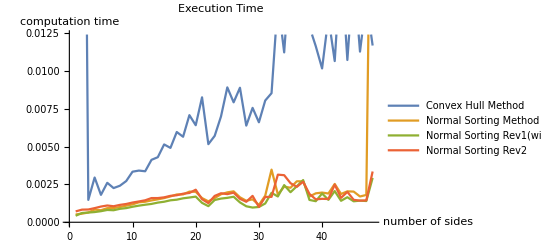

```mathematica
result=Table[robot =N[CirclePoints[i]];
obstacle =N[CirclePoints[i]];{AbsoluteTiming[findConvexHullCoordsConvexPolysAS[Polygon@obstacle,Polygon@robot]]⟦1⟧,
AbsoluteTiming[convexMinkowskiSum[robot,obstacle]]⟦1⟧,
AbsoluteTiming[convexMinkowskiSumRev1[robot,obstacle]]⟦1⟧,
AbsoluteTiming[convexMinkowskiSumRev2[robot,obstacle]]⟦1⟧}
,{i,3,50,1}];
ListLinePlot[Transpose@result,PlotLegends->{"Convex Hull Method","Normal Sorting Method","Normal Sorting Rev1(without Centorid)", "Normal Sorting Rev2"},AxesLabel->{"number of sides","computation time"},PlotLabel->"Execution Time"]
```

```mathematica
discretizeLine[{{x1_,y1_},{x2_,y2_}},step_]:=
({(x1+(x2-x1)*#),(y1+(y2-y1)*#)})&/@Range[0,1,step]
```

```mathematica
discretizePoly[poly_,step_]:=Module[{lineList},
lineList[list_]:=Partition[Append[list,First[list]],2,1];
Append[Flatten[discretizeLine[#,step]⟦1;;(1/step)-1⟧&/@lineList[poly],1],First@poly]
]
```

```mathematica
lineList[list_]:=Partition[Append[list,First[list]],2,1];
```

892

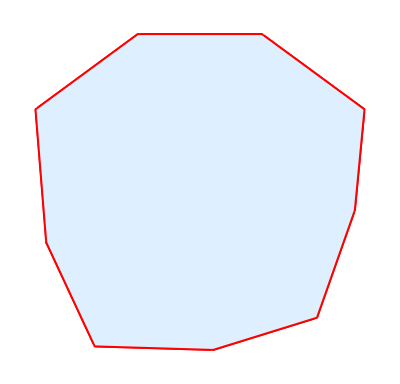

```mathematica
poly={{-3.4300000000000006,1.8049999999999997},{-2.9800000000000004,0.8379999999999996},{-1.8800000000000003,0.8049999999999997},{-0.9150000000000005,1.105},{-0.5630000000000006,2.105},{-0.47300000000000053,3.045},{-1.4250000000000005,3.745},{-2.5800000000000005,3.745},{-3.5300000000000007,3.045}};
p=discretizePoly[poly,0.01];
Length@p
Graphics[{Red,Point@p,LightBlue,Polygon@poly}]
```

```mathematica
Manipulate[
r=returnConvexPoly[pts⟦1;;4⟧];
Print@Length@r;
Graphics[{EdgeForm[Thin],LightBlue,Polygon@r,Red,Point[pts⟦2;;4⟧]}]
,{{pts,{{1.5, 2.44}, {1.41, 1.5}, {2.565, 1.5}, {2.465, 2.74}, 
  {1.7345, 2.79}, {-1.4, 1.5}, {-1.048, 2.5}, {-2, 3.2}, 
  {-2.95, 2.5}, {-2.5, 1.533}}},{-3.2,1.5},{3.2,3.2},
ControlType->Locator,Appearance->None}]
```

{{2.88588,1.48908},{3.24915,2.60711},{2.2981,3.2981},{1.34704,2.60711},{1.71031,1.48908}}

{{-1.71031,1.48908},{-1.34704,2.60711},{-2.2981,3.2981},{-3.24915,2.60711},{-2.88588,1.48908}}

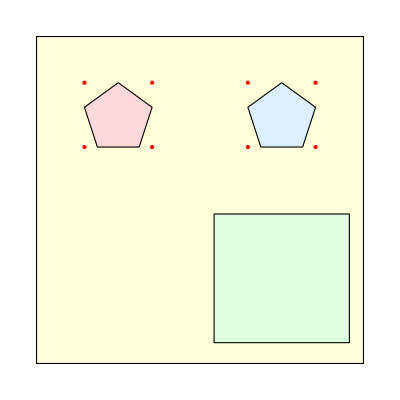

```mathematica
robo=(({2.2980970388562794,2.2980970388562794}+#)&/@CirclePoints[5])
obo=(({-2.2980970388562794,2.2980970388562794}+#)&/@CirclePoints[5])
minsum=(-Mean@obo+{2.2980970388562794,-2.2980970388562794}+#)&/@(convexMinkowskiSumRev2[robolimit,obolimit]);
Graphics[{EdgeForm[Thin],{LightYellow,Polygon@(6.5CirclePoints[4])},{LightBlue,Polygon@robo},
{(*Light*)Red,Point@({{obo⟦2⟧⟦1⟧,obo⟦1⟧⟦2⟧},{obo⟦2⟧⟦1⟧,obo⟦3⟧⟦2⟧},{obo⟦4⟧⟦1⟧,obo⟦3⟧⟦2⟧},{obo⟦4⟧⟦1⟧,obo⟦1⟧⟦2⟧}}),LightRed,Polygon@obo,Red,Point@robolimit},
{LightGreen,Polygon@minsum}}]
```

```mathematica
obolimit={{obo⟦2⟧⟦1⟧,obo⟦1⟧⟦2⟧},{obo⟦2⟧⟦1⟧,obo⟦3⟧⟦2⟧},{obo⟦4⟧⟦1⟧,obo⟦3⟧⟦2⟧},{obo⟦4⟧⟦1⟧,obo⟦1⟧⟦2⟧}}
robolimit=({2*2.2980970388562794,0}+#)&/@obolimit
```

{{-1.34704,1.48908},{-1.34704,3.2981},{-3.24915,3.2981},{-3.24915,1.48908}}

{{3.24915,1.48908},{3.24915,3.2981},{1.34704,3.2981},{1.34704,1.48908}}

```mathematica
-1.3470405225611257
```

```mathematica
{-3.249,1.489}
```

```mathematica
{3.249,3.298}
```